### spatio-spectral calculation of field

```mathematica
SetOptions[Plot,PlotHighlighting->None];
```

#### define local BW, central freq, spot size, no input chirp

To analyze the spatio-temporal properties of a spatially-chirped beam, it is necessary to find the local central frequency and bandwidth. We can then perform an analytic calculation of the pulse in the time domain by expanding the spectral phase around the local central frequency up to the second order  (φ_(0L), φ_(1L), φ_(2L)). Consider first a beam that is composed of a superposition of Gaussian beamlets with a transverse offset that varies linearly with frequency. This is the general structure of the amplitude of a beam with transverse chirp in the frequency domain. It will be the form of the input to the focusing lens. 
E(ω,x,y)=Exp[-(ω-ω_0)^2/Δω^2]Exp[-((x-α_L(ω-ω_0))^2+y^2)/w_L^2]
Here ω is the angular frequency, and the spectrum of width Δω is centered at ω_0. We will assume the local spot radius w_L is independent of frequency, and that the center of each beamlet is shifted in the x-direction by α_L(ω-ω_0). The parameters w_L and α_L will later be functions of the overall beam propagation direction z.

Notation: 
Δω is full beam bandwidth. 
w_L(z) is the local beamlet radius.
α_L(z)(ω-ω_0) describes the transverse offset in x for a beamlet centered at ω

Expand the function to get the local spectrum parameters:

```mathematica
Collect[(ω-ω0)^2/Δω^2+((x-αL(ω-ω0))/wL)^2,ω]
```

x^2/wL^2+(αL^2/wL^2+1/Δω^2) ω^2+(2 x αL ω0)/wL^2+(αL^2 ω0^2)/wL^2+ω0^2/Δω^2+ω (-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)

complete the square to get local frequency and bandwidth: 
a ω^2+b ω+c=a (ω^2+b/a ω)+c=a (ω+b/(2a))^2+c-b^2/(4a)
here, a=(α_L^2/w_L^2+1/Δω^2), b=(-(2 x α_L)/w_L^2-(2 α_L^2 ω_0)/w_L^2-(2 ω_0)/Δω^2), c=x^2/w_L^2+(2 x α_L ω_0)/w_L^2+(α_L^2 ω_0^2)/w_L^2+ω_0^2/Δω^2

Check this assignment of constants:

```mathematica
FullSimplify[(ω-ω0)^2/Δω^2+((x-αL(ω-ω0))/wL)^2-((αL^2/wL^2+1/Δω^2) (ω+(-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)/(2(αL^2/wL^2+1/Δω^2)))^2+x^2/wL^2+(2 x αL ω0)/wL^2+(αL^2 ω0^2)/wL^2+ω0^2/Δω^2-((-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)^2)/(4(αL^2/wL^2+1/Δω^2)))]
```

0

now define local bandwidth:
Δω_L=1/(√a)=√(1/(α_L^2/w_L^2+1/Δω^2))=Δω √(1/(1+(α_L^2 Δω^2)/w_L^2))
use this to define local β and beam aspect ratio:   
β_L=(α_L Δω)/w_L, β_BAL=√(1+β_L^2)
Δω_L=Δω √(1/β_BAL^2)=Δω/β_BAL
note that as the beamlet sizes and α vary in z, then β_L and β_BAL also depend on z. 
Check again, using these definitions of local bandwidth.

```mathematica
FullSimplify[((ω-ω0)^2/Δω^2+((x-αL(ω-ω0))/wL)^2-( ((ω+(-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)/(2(αL^2/wL^2+1/Δω^2)))^2)/ΔωL^2+x^2/wL^2+(2 x αL ω0)/wL^2+(αL^2 ω0^2)/wL^2+ω0^2/Δω^2-((-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)^2)/(4(αL^2/wL^2+1/Δω^2))))/.{ΔωL->Δω/βBAL}/.{βBAL->√(1+βL^2)}/.βL->(αL Δω)/wL]
```

0

define local central frequency:

note that since 1/(√a)=Δω_L=Δω/β_BAL, a=β_BAL^2/Δω^2

ω_(0,L)=-b/(2a)=-(-(2 x α_L)/w_L^2-(2 α_L^2 ω_0)/w_L^2-(2 ω_0)/Δω^2)/(2a)=((x α_L)/w_L^2+(α_L^2 ω_0)/w_L^2+ω_0/Δω^2)/(β_BAL^2/Δω^2)=((x α_L Δω^2)/w_L^2+(α_L^2 Δω^2 ω_0)/w_L^2+ω_0)/β_BAL^2=(β_L Δω x/w_L+β_L^2 ω_0+ω_0)/β_BAL^2
ω_(0,L)=(β_L Δω x/w_L+β_BAL^2 ω_0)/β_BAL^2=ω_0+β_L/β_BAL^2 x/w_L Δω

Again, check to make sure we haven’t made any mistakes:

```mathematica
FullSimplify[((ω-ω0)^2/Δω^2+((x-αL(ω-ω0))/wL)^2-( (ω-ω0L)^2/ΔωL^2+x^2/wL^2+(2 x αL ω0)/wL^2+(αL^2 ω0^2)/wL^2+ω0^2/Δω^2-((-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)^2)/(4(αL^2/wL^2+1/Δω^2))))/.{ΔωL->Δω/βBAL,ω0L->ω0+βL/βBAL^2 x/wL Δω}/.{βBAL->√(1+βL^2)}/.βL->(αL Δω)/wL]
```

0

The last term in the completion of the square has to do with the spatial distribution of the intensity: 
c-b^2/(4a)
reduce this by brute force:

```mathematica
ExpandAll[x^2/wL^2+(2 x αL ω0)/wL^2+(αL^2 ω0^2)/wL^2+ω0^2/Δω^2-((-(2 x αL)/wL^2-(2 αL^2 ω0)/wL^2-(2 ω0)/Δω^2)^2)/(4 (αL^2/wL^2+1/Δω^2))]
```

x^2/wL^2-(4 x^2 αL^2)/(wL^4 ((4 αL^2)/wL^2+4/Δω^2))+(2 x αL ω0)/wL^2-(8 x αL^3 ω0)/(wL^4 ((4 αL^2)/wL^2+4/Δω^2))-(8 x αL ω0)/(wL^2 ((4 αL^2)/wL^2+4/Δω^2) Δω^2)+(αL^2 ω0^2)/wL^2-(4 αL^4 ω0^2)/(wL^4 ((4 αL^2)/wL^2+4/Δω^2))-(4 ω0^2)/(((4 αL^2)/wL^2+4/Δω^2) Δω^4)+ω0^2/Δω^2-(8 αL^2 ω0^2)/(wL^2 ((4 αL^2)/wL^2+4/Δω^2) Δω^2)

```mathematica
FullSimplify[%/.{αL^2->β^2 wL^2/Δω^2,αL^3->αL β^2 wL^2/Δω^2,αL^4->β^4 wL^4/Δω^4}]
```

x^2/(wL^2 (1+β^2))

verify:

```mathematica
FullSimplify[((ω-ω0)^2/Δω^2+((x-αL(ω-ω0))/wL)^2-( (ω-ω0L)^2/ΔωL^2+x^2/(wL^2 βBAL^2)))/.{ΔωL->Δω/βBAL,ω0L->ω0+βL/βBAL^2 x/wL Δω}/.{βBAL->√(1+βL^2)}/.βL->(αL Δω)/wL]
```

0

this version uses α_L=γ_0 z, where γ_0 is the angular chirp rate, which itself is independent of z.

```mathematica
Clear[γ0,ω0L,βBAL,βL,ΔωL];
```

```mathematica
FullSimplify[((ω-ω0)^2/Δω^2+((x-z γ0 (ω-ω0))/wL)^2-( (ω-ω0L)^2/ΔωL^2+x^2/(wL^2 βBAL^2)))/.{ΔωL->Δω/βBAL,ω0L->ω0+βL/βBAL^2 x/wL Δω}/.{βBAL->√(1+βL^2)}/.βL->(γ0 z Δω)/wL]
```

0

so the overall spatially chirped beam radius is w_L β_BAL

Summary: 
By expanding this expression and grouping the spatially-dependent terms, we can express this amplitude function for a spatially-chirped beam as
E(ω,x,y)=Exp[-(ω-ω_0)^2/Δω^2]Exp[-((x-α_L(ω-ω_0))^2+y^2)/w_L^2]=Exp[-(ω-ω_(0,L))^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]. 
In this form, there is a local bandwidth Δω_L=Δω/β_BAL and central frequency ω_(0,L)=ω_0+β_L/β_BAL^2 x/w_0 Δω. These functions involve dimensionless parameters, the spatial chirp rate β_L=(α_L Δω)/w_L and the beam aspect ratio β_BAL=√(1+β_L^2). (The L in the subscripts are a notational reminder that these local parameters will vary with z.)
This expression for the amplitude of the spatially chirped beam represents the transverse chirp with a function α_L, which gives the local transverse shift of a beamlet at frequency ω: α_L(ω-ω_0). When α_L>0 and δω=ω-ω_0>0, the beamlet is shifted towards x>0. 

When we pass the beam with collimated beamlets into a lens, the ordering of the frequency components is preserved for z<0 (where z=0 is at the focal plane), then the ordering flips after the focus, z>0. If x_s=α_0 δω is the beamlet shift at the lens, we can define an angular chirp rate γ_0=-α_0/f. After the lens, γ_0 is fixed, and a beamlet that starts at x>0 before the lens will propagate with negative slope. Now we can define a local α_L so that x_s(z)=α_L(z)δω,  then x_s(z)=z γ_0 δω=-z α_0/f δω, so α_L(z)=z γ_0. At the lens, z=-f, we get x_s=α_0 δω as before. 
So if we rewrite the equations in terms of γ_0, 
Exp[-(ω-ω_0)^2/Δω^2]Exp[-((x-z γ_0(ω-ω_0))^2+y^2)/w_L^2]
Exp[-(ω-ω_(0,L))^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]
β_L=(α_L Δω)/w_L=(z γ_0 Δω)/w_L
ω_(0,L)=ω_0+β_L/β_BAL^2 x/w_0 Δω

#### express tilted Gaussian beam in terms of γ (old)

For SSTF focusing, each frequency component is a Gaussian beam tilted at a frequency-dependent angle:  
E(x,y,z,ω)=E_0 w_0/(w(z))Exp[-(ω -ω_0)^2/Δω^2]Exp[-((x-z Tan[θ_x])^2+y^2)/(w(z))^2]Exp[ⅈ ω/c(Sin[θ_x]x+Cos[θ_x]z)-ⅈ η(z)+ⅈ ω/c Cos[θ_x]((x-z Tan[θ_x])^2+y^2)/(2 R(z))] 
Here, we will ignore and frequency dependence to the beam waist w_0 and the Rayleigh range, so that the beam 1/ⅇ^2 radius w, the wavefront curvature R, and the Gouy phase η=tan^-1(z/z_R) are only functions of z.  We will define and angular dispersion rate γ through the expression Tan[θ_x(ω)]=γ(ω-ω_0)=γ δω. For a beam with transverse chirp at the lens, so that the beamlets have frequency-dependent shifts x_s=α(ω-ω_0)≡α δω, the angular chirp is γ δω=-(α δω)/f≡Tan[θ_x(ω)]. We can then write 
Cos[θ_x(ω)]=1/(√(1+(γ δω)^2))
Sin[θ_x(ω)]=(γ  δω)/(√(1+(γ δω)^2)), 
which allow us to express the tilted Gaussian beams in terms of γ: 
E(x,y,z,ω)=E_0 w_0/(w(z))Exp[-(ω -ω_0)^2/Δω^2]Exp[-((x-z γ δω)^2+y^2)/(w(z))^2]Exp[ⅈ ω/c((γ  δω)/(√(1+(γ δω)^2))x+1/(√(1+(γ δω)^2))z)-ⅈ η(z)+ⅈ ω/c 1/(√(1+(γ δω)^2))((x-z γ δω)^2+y^2)/(2 R(z))] 
As this beam propagates, the transverse chirp and the beam sizes evolve. With respect to our expressions for a spatially chirped beam, we can define the local shift parameter as α_L=z γ, and the local spatial chirp rate β_L=(α_L Δω)/(w(z))=(γ z Δω)/(w(z)). This formulation assumes that there is no transverse chirp at the wavelength crossing plane. Following that approach, the amplitude can be rewritten in terms of these local parameters: 
E(ω,x,y)=E_0 w_0/(w(z))Exp[-(ω-ω_(0,L))^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]Exp[-ⅈ η(z)]Exp[ⅈ ω/c((γ  δω)/(√(1+(γ δω)^2))x+1/(√(1+(γ δω)^2))z+1/(√(1+(γ δω)^2))((x-z γ δω)^2+y^2)/(2 R(z)))]

#### expand on δωL (old)

Since the Fourier transform for a Gaussian pulse with first and second order dispersion can be calculated analytically, the next step is to expand the spectral phase around the local central frequency: 
ω_(0L)=ω_0+β/β_BA^2 x/w_0 Δω, so that δω_L=ω-ω_(0L) is a small parameter. 
We will include optional input second order chirp, 1/(2!)(Φ_2(ω-ω_0))^2=1/2 Φ_2 δω^2, where Φ_2=(∂_ω)^2 Φ and δω=ω-ω_0.
In the expression for the spectral phase, we let ω->δω_L+ω_(0L), and δω=δω_L+ω_(0L)-ω_0≡δω_L+dω_(0L), yielding the spectral phase
φ(ω)=(δω_L+ω_(0L))/(c √(1+(γ (δω_L+dω_(0L)))^2))(γ (δω_L+dω_(0L))x+z+1/(2 R(z))((x-z γ (δω_L+dω_(0L)))^2)^2+y^2)+1/2(Φ_2(δω_L+dω_(0L)))^2-η(z)

Noting that we assume z_R and R(z) are assumed to be frequency-independent, we expand the spectral phase to second order in δω_L.

```mathematica
Clear[c];
eq1=Series[(δωL+ω0L)/(c √(1+(γ (δωL+dω0L))^2))((γ  (δωL+dω0L)x+z)+((x-z γ (δωL+dω0L))^2+y^2)/(2 R))+1/2 Φ2(δωL+dω0L)^2,{δωL,0,2}]
```

((dω0L^2 Φ2)/2+((z+dω0L x γ+(y^2+(x-dω0L z γ)^2)/(2 R)) ω0L)/(c √(1+dω0L^2 γ^2)))+(dω0L Φ2+((z+dω0L x γ+(y^2+(x-dω0L z γ)^2)/(2 R))/(√(1+dω0L^2 γ^2))+((x γ-(z γ (x-dω0L z γ))/R)/(√(1+dω0L^2 γ^2))-(dω0L γ^2 (z+dω0L x γ+(y^2+(x-dω0L z γ)^2)/(2 R)))/((1+dω0L^2 γ^2)^(3/2))) ω0L)/c) δωL+(Φ2/2+1/c((x γ-(z γ (x-dω0L z γ))/R)/(√(1+dω0L^2 γ^2))-(dω0L γ^2 (z+dω0L x γ+(y^2+(x-dω0L z γ)^2)/(2 R)))/((1+dω0L^2 γ^2)^(3/2))+((z^2 γ^2)/(2 R √(1+dω0L^2 γ^2))-(dω0L γ^2 (x γ-(z γ (x-dω0L z γ))/R))/((1+dω0L^2 γ^2)^(3/2))+((-γ^2+2 dω0L^2 γ^4) (z+dω0L x γ+(y^2+(x-dω0L z γ)^2)/(2 R)))/(2 (1+dω0L^2 γ^2)^(5/2))) ω0L)) δωL^2+O[δωL]^3

Re-state definitions: 
ω_(0L)=ω_0+β/β_BA^2 x/w_0 Δω			local central frequency
dω_(0L)=ω_(0L)-ω_0=β_L/β_BAL^2 x/w_0 Δω	difference between local freq and ω_0
β_L=(γ z Δω)/(w_L(z))=(γ z Δω)/(w_0 √(1+z^2/z_R^2))			local transverse chirp parameter 
We could try defining 1/√(1+γ^2 dω0L^2)=Cos[θL] to try to simplify. The expressions don’t break down into much simpler form though.

### time-domain calculation: expand around ω_(0L). Original formulation (old). defining functions that can be evaluated numerically

#### evaluate expansions

this is based on assuming a sweep of tilted Gaussian beams at the focus instead of propagating all the way from the lens

set z=0 at beamlet focus
this version does not yet account for a shift z_c of the wavelength crossing plane from the beamlet focal plane
E(x,y,z,ω)=w_0/(w(z))Exp[-δω_L^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]Exp[ⅈ ((δω_L+ω_(0,L))/c((γ  (δω_L+dω_(0,L)))/(√(1+(γ (δω_L+dω_(0,L)))^2))x+1/(√(1+(γ (δω_L+dω_(0,L)))^2))z)-η(z)+(δω_L+ω_(0,L))/c 1/(√(1+(γ (δω_L+dω_(0,L)))^2))((x-α_L (δω_L+dω_(0,L)))^2+y^2)/(2 R(z))+1/2(Φ_2(δω_L+dω_(0,L)))^2)] 
auxiliary functions: 
Δω_L=Δω/β_BAL			local bandwidth
ω_(0,L)=ω_0+β_L/β_BAL^2 x/w_0 Δω	local central frequency
 β_L=(α_L Δω)/w_L, β_BAL=√(1+β_L^2)
α_L=γ z				here is assumption of wavelength crossing plane = beamlet waist plane
δω_L=ω-ω_(0,L)
dω_(0,L)=ω_(0,L)-ω_0=β_L/β_BAL^2 x/w_0 Δω

we are neglecting any ω dependence of the Rayleigh range. 
exp[ⅈ k z] term is included, so the pulse should move in z

do a series expansion of the spectral phase around ω_(0L)
I cut and paste the 3 different terms below to define the functions.

```mathematica
Clear[c];
eq1=Series[(δωLoc+ω0Loc)/c((γ  (δωLoc+dω0Loc))/(√(1+(γ (δωLoc+dω0Loc))^2))x+1/(√(1+(γ (δωLoc+dω0Loc))^2))z)+(δωLoc+ω0Loc)/c 1/(√(1+(γ (δωLoc+dω0Loc))^2))Rinv((x-z γ (δωLoc+dω0Loc))^2+y^2)/2+1/2 ϕ2In(δωLoc+dω0Loc)^2,{δωLoc,0,2}]
```

((dω0Loc^2 ϕ2In)/2+((z+dω0Loc x γ) ω0Loc)/(c √(1+dω0Loc^2 γ^2))+(Rinv (y^2+(x-dω0Loc z γ)^2) ω0Loc)/(2 c √(1+dω0Loc^2 γ^2)))+(dω0Loc ϕ2In+((z+dω0Loc x γ)/(√(1+dω0Loc^2 γ^2))+((x γ-dω0Loc z γ^2) ω0Loc)/((1+dω0Loc^2 γ^2)^(3/2)))/c+(Rinv ((y^2+(x-dω0Loc z γ)^2)/(√(1+dω0Loc^2 γ^2))+(-(2 z γ (x-dω0Loc z γ))/(√(1+dω0Loc^2 γ^2))-(dω0Loc γ^2 (y^2+(x-dω0Loc z γ)^2))/((1+dω0Loc^2 γ^2)^(3/2))) ω0Loc))/(2 c)) δωLoc+(ϕ2In/2+((x γ-dω0Loc z γ^2)/((1+dω0Loc^2 γ^2)^(3/2))+((-z γ^2-3 dω0Loc x γ^3+2 dω0Loc^2 z γ^4) ω0Loc)/(2 (1+dω0Loc^2 γ^2)^(5/2)))/c+1/(2 c)Rinv (-(2 z γ (x-dω0Loc z γ))/(√(1+dω0Loc^2 γ^2))-(dω0Loc γ^2 (y^2+(x-dω0Loc z γ)^2))/((1+dω0Loc^2 γ^2)^(3/2))+((2 dω0Loc z γ^3 (x-dω0Loc z γ))/((1+dω0Loc^2 γ^2)^(3/2))+(z^2 γ^2)/(√(1+dω0Loc^2 γ^2))+((-γ^2+2 dω0Loc^2 γ^4) (y^2+(x-dω0Loc z γ)^2))/(2 (1+dω0Loc^2 γ^2)^(5/2))) ω0Loc)) δωLoc^2+O[δωLoc]^3

#### calculate spatio-spectral field

to do a direct comparison, here is the spatio-spectral version starting from the tilted Gaussian beamlets

```mathematica
Aω[x_,y_,z_,ω_,ω0_,δω_,γ_,w0_,zc_,ϕ2In_]:=w0/w Exp[-δωLoc^2/ΔωLoc^2] Exp[-x^2/(w^2 βBALoc^2)]Exp[-y^2/w^2]Exp[-ⅈ ArcTan[z/((ω0 w0^2)/(2 c))]]Exp[ⅈ((δωLoc+ω0Loc)/c((γ  (δωLoc+dω0Loc))/(√(1+(γ (δωLoc+dω0Loc))^2))x+1/(√(1+(γ (δωLoc+dω0Loc))^2))z)+(δωLoc+ω0Loc)/c 1/(√(1+(γ (δωLoc+dω0Loc))^2))Rinv((x-z γ (δωLoc+dω0Loc))^2+y^2)/2)]Exp[ⅈ 1/(2!)ϕ2In(ω-ω0)^2]/.{w->wz[z,w0,ω0],Rinv->Rinvz[z,w0,ω0],βBALoc->βBAL[z,ω0,δω,γ,w0],dω0Loc->dω0L[x,z,ω0,δω,γ,w0],ω0Loc->ω0L[x,z,ω0,δω,γ,w0],δωLoc->ω-ω0L[x,z,ω0,δω,γ,w0],ΔωLoc->ΔωL[z,ω0,δω,γ,w0]};
```

#### calculate the spatio-temporal field

now put this into the full expression and do the inverse Fourier transform to get to t-space. 
using dω=ω-ω_0 as the transform variable, δω is the bandwidth, consistent with above notation. 
not including third-order dispersion, since that is harder to include in the transform. 
to compare the two results, we’ll need to translate the lens input chirp to a γ for angular chirp, and use the focal spot size instead of the input beam size/focal length combination. 
E(x,y,z,ω)=w_0/(w(z))Exp[-δωL^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]Exp[ⅈ (φ0+φ1 δωL+φ2 δωL^2-η(z))]

```mathematica
Clear[dω,w,zR,ω0,c,w0,Rz,wz, φ0Loc,φ1Loc,φ2Loc];
```

do invFT, for this step, pull out terms that don’t depend on δωL

```mathematica
InverseFourierTransform[Exp[-δωLoc^2/ΔωLoc^2]Exp[ⅈ(φ0Loc+φ1Loc δωLoc+φ2Loc  δωLoc^2)],δωLoc,t,FourierParameters->{1,1}]
```

(ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))

now assemble full expression of time-domain field
(π w_0^2)/λ=(2π w_0^2)/(2λ)=(ω_0 w_0^2)/(2c)
apparently, zc isn’t used (might be an offset of crossing and focal planes)

```mathematica
At[x_,y_,z_,t_,ω0_,δω_,γ_,w0_,zc_,ϕ2In_]=w0/w Exp[-x^2/(w^2 βBALoc^2)]Exp[-y^2/w^2]Exp[-ⅈ ArcTan[z/zR]](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))/.{w->wz[z,w0,ω0],zR->(ω0 w0^2)/(2c),βBALoc->βBAL[z,ω0,δω,γ,w0],φ0Loc->φ0L[x,y,z,ω0,δω,γ,w0,ϕ2In],φ1Loc->φ1L[x,y,z,ω0,δω,γ,w0,ϕ2In],φ2Loc->φ2L[x,y,z,ω0,δω,γ,w0,ϕ2In],ΔωLoc->ΔωL[z,ω0,δω,γ,w0]};
```

#### define the auxiliary functions

extract φ0, φ1, φ2 coefficients from series expansion
using δω for full laser bandwidth instead of Δω to be consistent with the rest of this notebook

```mathematica
φ0L[x_,y_,z_,ω0_,δω_,γ_,w0_,ϕ2In_]=((dω0Loc^2 ϕ2In)/2+((z+dω0Loc x γ) ω0Loc)/(c √(1+dω0Loc^2 γ^2))+(Rinv (y^2+(x-dω0Loc z γ)^2) ω0Loc)/(2 c √(1+dω0Loc^2 γ^2)))/.{Rinv->Rinvz[z,w0,ω0],dω0Loc->dω0L[x,z,ω0,δω,γ,w0],ω0Loc->ω0L[x,z,ω0,δω,γ,w0]};
φ1L[x_,y_,z_,ω0_,δω_,γ_,w0_,ϕ2In_]=(dω0Loc ϕ2In+((z+dω0Loc x γ)/(√(1+dω0Loc^2 γ^2))+((x γ-dω0Loc z γ^2) ω0Loc)/((1+dω0Loc^2 γ^2)^(3/2)))/c+(Rinv ((y^2+(x-dω0Loc z γ)^2)/(√(1+dω0Loc^2 γ^2))+(-(2 z γ (x-dω0Loc z γ))/(√(1+dω0Loc^2 γ^2))-(dω0Loc γ^2 (y^2+(x-dω0Loc z γ)^2))/((1+dω0Loc^2 γ^2)^(3/2))) ω0Loc))/(2 c)) /.{Rinv->Rinvz[z,w0,ω0],dω0Loc->dω0L[x,z,ω0,δω,γ,w0],ω0Loc->ω0L[x,z,ω0,δω,γ,w0]};
φ2L[x_,y_,z_,ω0_,δω_,γ_,w0_,ϕ2In_]=(ϕ2In/2+((x γ-dω0Loc z γ^2)/((1+dω0Loc^2 γ^2)^(3/2))+((-z γ^2-3 dω0Loc x γ^3+2 dω0Loc^2 z γ^4) ω0Loc)/(2 (1+dω0Loc^2 γ^2)^(5/2)))/c+1/(2 c)Rinv (-(2 z γ (x-dω0Loc z γ))/(√(1+dω0Loc^2 γ^2))-(dω0Loc γ^2 (y^2+(x-dω0Loc z γ)^2))/((1+dω0Loc^2 γ^2)^(3/2))+((2 dω0Loc z γ^3 (x-dω0Loc z γ))/((1+dω0Loc^2 γ^2)^(3/2))+(z^2 γ^2)/(√(1+dω0Loc^2 γ^2))+((-γ^2+2 dω0Loc^2 γ^4) (y^2+(x-dω0Loc z γ)^2))/(2 (1+dω0Loc^2 γ^2)^(5/2))) ω0Loc))/.{Rinv->Rinvz[z,w0,ω0],dω0Loc->dω0L[x,z,ω0,δω,γ,w0],ω0Loc->ω0L[x,z,ω0,δω,γ,w0]};
```

Δω_L=Δω/β_BAL
ω_(0,L)=ω_0+β_L/β_BAL^2 x/w_0 Δω
dω_(0,L)=ω_(0,L)-ω_0=β_L/β_BAL^2 x/w_0 Δω
 β_L=(α_L Δω)/w_L, β_BAL=√(1+β_L^2)
α_L=γ z

```mathematica
βL[z_,ω0_,Δω_,γ_,w0_]:=(z γ Δω)/wz[z,w0,ω0];
βBAL[z_,ω0_,Δω_,γ_,w0_]:=√(1+βL[z,ω0,Δω,γ,w0]^2);
ΔωL[z_,ω0_,Δω_,γ_,w0_]:=Δω/βBAL[z,ω0,Δω,γ,w0];
ω0L[x_,z_,ω0_,Δω_,γ_,w0_]:=ω0+βL[z,ω0,Δω,γ,w0]/βBAL[z,ω0,Δω,γ,w0]^2 x/w0 Δω;
dω0L[x_,z_,ω0_,Δω_,γ_,w0_]:=ω0L[x,z,ω0,Δω,γ,w0]-ω0;
```

```mathematica
wz[z_,w0_,ω0_]:=w0 √(1+z^2/(((ω0 w0^2)/(2 c))^2));
Rz[z_,w0_,ω0_]:=z(1+(((ω0 w0^2)/(2 c))^2)/z^2);
Rinvz[z_,w0_,ω0_]:=(z/(z^2+((ω0 w0^2)/(2 c))^2));
```

#### spatio-temporal intensity

```mathematica
FullSimplify[At[x,y,z,t,ω0,δω,γ,w0,0,ϕ2In],Assumptions->{Im[ϕ2In]==0,Im[x]==0,Im[y]==0,Im[z]==0,Im[t]==0,ω0>0,w0>0,δω>0,Im[γ]==0,c>0}]
```

$Aborted

### derivation of the field in the time-domain

expand around ω_(0L), defining functions that can be evaluated numerically 
This new formulation is based on beam waists 1f behind lens

#### calculate spatio-spectral field

to do a direct comparison, here is the spatio-spectral version starting from the tilted Gaussian beamlets
so far, zc isn’t used
aux functions defined below

this is based on assuming a sweep of tilted Gaussian beams at the focus instead of propagating all the way from the lens
z=0 is defined to be at the beamlet focus. This version does not yet account for a shift z_c of the wavelength crossing plane from the beamlet focal plane.
E(x,y,z,ω)=w_0/(w(z))Exp[-δω_L^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]Exp[ⅈ (ω/c(Tan[θ_x]x+(1-1/2 Tan[θ_x]^2)z)-η(z)+ω/c((x-γ_0 z (ω-ω_0))^2+y^2)/(2 R(z))+1/2(Φ_2(ω-ω_0))^2)] 
with Tan[θ_x]=γ_0(ω-ω_0)
E(x,y,z,ω)=w_0/(w(z))Exp[-(ω-ω_(0L))^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]Exp[ⅈ (ω/c(γ_0(ω-ω_0)x+(1-1/2(γ_0^2(ω-ω_0))^2)z)-η(z)+ω/c((x-γ_0 z (ω-ω_0))^2+y^2)/(2 R(z))+1/2(Φ_2(ω-ω_0))^2)] 
auxiliary functions: 
Δω_L=Δω/β_BAL			local bandwidth
ω_(0,L)=ω_0+β_L/β_BAL^2 x/w_0 Δω	local central frequency
 β_L=(α_L Δω)/w_L, β_BAL=√(1+β_L^2)
 α_L=z γ	
 by construction, the wavelength crossing plane = beamlet waist plane

To simplify, neglecting any ω dependence of the Rayleigh range. 
Since the exp[ⅈ k z] term is included, so the pulse should move in z.

```mathematica
AωTst[x_,y_,z_,ω_,ω0_,Δω_,γ_,w0_,zc_,ϕ2In_]:=w0/w Exp[-δωLoc^2/ΔωLoc^2] Exp[-x^2/(w^2 βBALoc^2)]Exp[-y^2/w^2]Exp[-ⅈ ArcTan[z/((ω0 w0^2)/(2 c))]]Exp[ⅈ(ω/c(γ(ω-ω0)x+(1-1/2 γ^2(ω-ω0)^2)z)+ω/(2c)Rinv((x-z γ (ω-ω0))^2+y^2))]Exp[ⅈ 1/(2!)ϕ2In(ω-ω0)^2]/.{w->wz[z,w0,ω0],Rinv->Rinvz[z,w0,ω0],βBALoc->βBAL[z,ω0,Δω,γ,w0],dω0Loc->dω0L[x,z,ω0,Δω,γ,w0],ω0Loc->ω0L[x,z,ω0,Δω,γ,w0],δωLoc->ω-ω0L[x,z,ω0,Δω,γ,w0],ΔωLoc->ΔωL[z,ω0,Δω,γ,w0]};
```

#### evaluate spectral phase expansion around the local central frequency

Gather the phase terms, then do a series expansion of the spectral phase around ω_(0L) up to and including 2nd order. We will then cut and paste the coefficients of the 3 different orders below to define the spectral phase functions. 
   Instead of manually writing out δωLoc=ω-ω_(0L) and expanding on small δωLoc, just expand directly around ω_(0L)

The spectral phase term from the spatio-spectral field is:    
φ(x,y,z,ω)=ω/c(γ_0(ω-ω_0)x+(1-1/2(γ_0^2(ω-ω_0))^2)z)-η(z)+ω/c 1/2((x-γ_0 z (ω-ω_0))^2+y^2)R_inv(z)+1/2(Φ_(2in)(ω-ω_0))^2
using Rinv=1/R(z) to avoid dividing by zero at focus.

```mathematica
Clear[c];
eq1=Series[ω/c(γ(ω-ω0)x+(1-1/2 γ^2(ω-ω0)^2)z)+ω/c Rinv((x-z γ (ω-ω0))^2+y^2)/2+1/2 ϕ2In(ω-ω0)^2,{ω,ω0Loc,2}]//Normal
```

(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2) ω0Loc)/(2 c)+1/2 ϕ2In (-ω0+ω0Loc)^2+1/(2 c)(ω-ω0Loc)^2 (2 x γ-2 Rinv x z γ+c ϕ2In+2 z γ^2 ω0-2 Rinv z^2 γ^2 ω0-3 z γ^2 ω0Loc+3 Rinv z^2 γ^2 ω0Loc)+(ω0Loc (x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2)))/c+(ω-ω0Loc) (-ϕ2In (ω0-ω0Loc)+(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2-2 z γ (x+z γ (ω0-ω0Loc)) ω0Loc))/(2 c)+((x γ+z γ^2 (ω0-ω0Loc)) ω0Loc+x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))/c)

This breaks out into three terms: 
ϕ(z)=φ_(0L)+(ω-ω0Loc)φ_(1L)+(ω-ω0Loc)^2 φ_(2L)
note that we’re absorbing the 1/2! into φ_(2L)
(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2) ω0Loc)/(2 c)+1/2 ϕ2In (-ω0+ω0Loc)^2
+1/(2 c)(ω-ω0Loc)^2 (2 x γ-2 Rinv x z γ+c ϕ2In+2 z γ^2 ω0-2 Rinv z^2 γ^2 ω0-3 z γ^2 ω0Loc+3 Rinv z^2 γ^2 ω0Loc)
+(ω0Loc (x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2)))/c
+(ω-ω0Loc) (-ϕ2In (ω0-ω0Loc)+(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2-2 z γ (x+z γ (ω0-ω0Loc)) ω0Loc))/(2 c)+((x γ+z γ^2 (ω0-ω0Loc)) ω0Loc+x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))/c)

Extracting the terms from this expression: 
φ_(0L)=(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2) ω0Loc)/(2 c)+1/2 ϕ2In (-ω0+ω0Loc)^2+1/c ω0Loc (x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))
φ_(1L)=-ϕ2In (ω0-ω0Loc)+(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2-2 z γ (x+z γ (ω0-ω0Loc)) ω0Loc))/(2 c)+((x γ+z γ^2 (ω0-ω0Loc)) ω0Loc+x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))/c
φ_(2L)=1/(2 c)(2 x γ-2 Rinv x z γ+c ϕ2In+2 z γ^2 ω0-2 Rinv z^2 γ^2 ω0-3 z γ^2 ω0Loc+3 Rinv z^2 γ^2 ω0Loc)
These will be put into functions later when we define the spatio-temporal field.

#### do the inverse FT to get the general expression in the time domain

now put this into the full expression and do the inverse Fourier transform to get to t-space. 
using dω=ω-ω_0 as the transform variable, δω is the bandwidth, consistent with above notation. 
not including third-order dispersion, since that is harder to include in the transform. 
to compare the two results, we’ll need to translate the lens input chirp to a γ for angular chirp, and use the focal spot size instead of the input beam size/focal length combination. 
E(x,y,z,ω)=w_0/(w(z))Exp[-δωL^2/Δω_L^2]Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]Exp[ⅈ (φ0+φ1 δωL+φ2 δωL^2-η(z))]

```mathematica
Clear[dω,w,zR,ω0,c,w0,Rz,wz, φ0Loc,φ1Loc,φ2Loc];
```

do invFT, for this step, pull out terms that don’t depend on δωL

```mathematica
InverseFourierTransform[Exp[-δωLoc^2/ΔωLoc^2]Exp[ⅈ(φ0Loc+φ1Loc δωLoc+φ2Loc  δωLoc^2)],δωLoc,t,FourierParameters->{1,1}]
```

(ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))

the full field (unnormalized) is
w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))

#### normalize the spatio-temporal field

As written, the function we have for the spatio-temporal field has units of 1/time. 
w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))
the units come from the √(1/ΔωLoc^2-ⅈ φ2Loc) factor. Since for a Gaussian spectrum the transform-limited pulse duration is τ=2/Δω, 1/ΔωLoc=τ_loc/2, where τ_loc is the local transform limited pulse duration within the spatially chirped pulse. φ2Loc is the local group delay dispersion, so we could rewrite this as τ_loc/2 √(1-ⅈ φ2Loc ΔωLoc^2). As φ2Loc increases, the pulse duration increases. The real part of this function in the denominator of the main expression will adjust the peak field strength (or intensity) as the pulse duration changes due to the chirp.

What we want in a normalized function is to multiply by a constant so that when we integrate over the absolute value squared on x,y,t we get the pulse energy. We can evaluate this at any z-plane, then so it is simplest to choose to evaluate it at z=0. Most of the auxiliary functions will simplify considerably. 
1. The φ0Loc phase will have no effect on the normalization, since we are evaluating Abs[A_t]^2
2. w_L=w(z), w(z=0)=w_0
3. β_L=(α_L Δω)/w_L=(z γ Δω)/w_L, since α_L=z γ, so at z=0, β_L=0 and β_BAL=√(1+β_L^2)=1 (β and β_BA are measures of the transverse spatial chirp, but all frequency components are overlapped at focus). 
4. Δω_L=Δω/β_BAL, so at z=0, Δω_L=Δω (this means that at focus the full bandwidth is present)
Now put these simplifications in and see what is left: 
Exp[-x^2/w_0^2-y^2/w_0^2](ⅇ^(-ⅈ (Δω^2 (t-φ1Loc)^2)/(4 ⅈ+4 Δω^2 φ2Loc)))/(2 √π √(1/Δω^2-ⅈ φ2Loc))
evaluate the local group delay at focus: this is the pulse front tilt
φ1L= -ϕ2In (ω0-ω0Loc)+(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2-2 z γ (x+z γ (ω0-ω0Loc)) ω0Loc))/(2 c)+((x γ+z γ^2 (ω0-ω0Loc)) ω0Loc+x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))/c
we will choose the added input chirp to be zero ϕ2In=0
at z=0, Rinv=0 (flat wavefront),  ω0Loc=ω0
therefore: φ1L= (x γ ω0)/c
similarly, 
φ2L=(x γ)/c
with these, the field at focus is: 
Exp[-(x^2+y^2)/w_0^2](ⅇ^(-ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(4 ⅈ+4 Δω^2 (x γ)/c)))/(2 √π √(1/Δω^2-ⅈ (x γ)/c))

The next step is to calculate Abs[ ]^2
Exp[-(x^2+y^2)/w_0^2](ⅇ^(-ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(4 ⅈ+4 Δω^2 (x γ)/c)))/(2 √π √(1/Δω^2-ⅈ (x γ)/c))Exp[-(x^2+y^2)/w_0^2](ⅇ^(+ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(-4 ⅈ+4 Δω^2 (x γ)/c)))/(2 √π √(1/Δω^2+ⅈ (x γ)/c))
simplify by gathering terms: 
1/(4π √(1/Δω^4+((x γ)/c)^2))Exp[-2(x^2+y^2)/w0^2]ⅇ^(-ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(4 ⅈ+4 Δω^2 (x γ)/c))ⅇ^(+ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(-4 ⅈ+4 Δω^2 (x γ)/c))
now simplify exponent:

```mathematica
FullSimplify[-ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(4 ⅈ+4 Δω^2 (x γ)/c)+ⅈ (Δω^2 (t-(x γ ω0)/c)^2)/(-4 ⅈ+4 Δω^2 (x γ)/c),Assumptions->{c>0,w0>0,Im[y]==0,Im[x]==0,Im[γ]==0,Δω>0,Im[t]==0,ω0>0}]
```

-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4))

now at focus  Abs[ A_t]^2 is
1/(4π √(1/Δω^4+((x γ)/c)^2))Exp[-2(x^2+y^2)/w0^2]ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4)))
This is the exact expression for the tilted pulse at focus.

Now we can integrate to get the normalization constant. let’s multiply this by a constant (CC), then we can integrate over x,y,t to get the pulse energy, ℰ_0: 
ℰ_0=CC∫∫∫1/(4π √(1/Δω^4+((x γ)/c)^2))Exp[-2(x^2+y^2)/w0^2]ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4)))ⅆxⅆyⅆt
integrate over time first:

```mathematica
Integrate[CC/(4π √(1/Δω^4+((x γ)/c)^2))Exp[-2(x^2+y^2)/w0^2] ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4))),{t,-∞,∞},Assumptions->{c>0,w0>0,Im[y]==0,Im[x]==0,Im[γ]==0,Δω>0,ω0>0}]
```

(CC ⅇ^(-(2 (x^2+y^2))/w0^2) Δω)/(2 √(2 π))

now integrate over x,y:

```mathematica
Integrate[(CC ⅇ^(-(2 (x^2+y^2))/w0^2) Δω)/(2 √(2 π)),{x,-∞,∞},{y,-∞,∞},Assumptions->{c>0,w0>0,Im[γ]==0,Δω>0,ω0>0}]
```

1/4 CC √(π/2) w0^2 Δω

Finally, we set this equal to the energy, ℰ_0, and determine the normalization constant. 
ℰ_0=1/4 CC √(π/2) w0^2 Δω,
CC =(4 ℰ_0)/(√(π/2) w0^2 Δω)
The way we defined CC is so that the intensity at focus is
I(x,y,z=0,t)=CC Abs[A_t[x,y,z=0,t]]^2
So we can use this constant to define the intensity at focus as: 
I(x,y,z=0,t)=(4 ℰ_0)/(√(π/2) w0^2 Δω)1/(4π √(1/Δω^4+((x γ)/c)^2))Exp[-2(x^2+y^2)/w0^2]ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4)))
Optionally, we can simplify this, noting that the transform-limited pulse duration τ_0=2/Δω
I(x,y,z=0,t)=ℰ_0/(√(π/2) π w0^2 τ_0 Δω^2/2)1/(√(1/Δω^4+((x γ)/c)^2))Exp[-2(x^2+y^2)/w0^2]ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4)))
I(x,y,z=0,t)=ℰ_0/(√(π/8) π w_0^2 τ_0)1/(√(1+((x γ)/c)^2 Δω^4))Exp[-2(x^2+y^2)/w_0^2]ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4)))
verify normalization by integrating:

```mathematica
Integrate[ℰ0/(√(π/8) π w0^2 2/Δω)1/(√(1+((x γ)/c)^2 Δω^4))Exp[-2(x^2+y^2)/w0^2] ⅇ^(-(Δω^2 (c t-x γ ω0)^2)/(2 (c^2+x^2 γ^2 Δω^4))),{t,-∞,∞},Assumptions->{c>0,w0>0,Im[y]==0,Im[x]==0,Im[γ]==0,Δω>0,ω0>0}]
```

(2 ⅇ^(-(2 (x^2+y^2))/w0^2) ℰ0)/(π w0^2)

```mathematica
Integrate[(2 ⅇ^(-(2 (x^2+y^2))/w0^2) ℰ0)/(π w0^2),{x,-∞,∞},{y,-∞,∞},Assumptions->{c>0,w0>0,Im[γ]==0,Δω>0,ω0>0}]
```

ℰ0

```mathematica
(*W(z)and Subscript[W, L] are same*)
```

So this works. The normalization should be valid at any z-plane. 
Finally, we can multiply the field by  √CC to normalize it: 
√((4 ℰ_0)/(√(π/2) w0^2 Δω))w_0/w_L Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))
This is our new normalized function for the field. We will want to verify it with numerical integration. 
the peak intensity would be: 
√((4 ℰ_0)/(√(π/2) w0^2 Δω))1/(2 √π √(1/ΔωLoc^2))
((4 ℰ_0)/(√(π/2) w0^2 Δω)Δω^2)/(4 π)=(4 ℰ_0)/(√(2π) π  w0^2)Δω/2
the transform limited pulse duration is τ=2/Δω
peak intensity is ((4 ℰ_0)/(√(π/2) w0^2 Δω)Δω^2)/(4 π)=4/(π  w0^2 τ)ℰ_0/(π  w0^2 τ)

#### define the normalized complex spatio-temporal field

From the previous section, the normalized time-domain electric field (not the vector potential) is: 
A_t[x,y,z,t]=√((4 ℰ_0)/(√(π/2) w0^2 Δω))Exp[-ⅈ ω_(0Loc)t]w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))
where we are multiplying by the local carrier: Exp[-ⅈ ω_(0Loc)t]
now assemble full expression of time-domain field
The Rayleigh range is evaluated at the central frequency: z_R=(π w_0^2)/λ=(2π w_0^2)/(2λ)=(ω_0 w_0^2)/(2c)
zc is a placeholder for the an offset between the focal and wavelength crossing planes, and is not included here. 
Relative to an earlier version, this At[ ] function eliminates zc as an argument and adds the pulse energy ℰ_0.

```mathematica
At[x_,y_,z_,t_,ω0_,Δω_,γ_,w0_,ϕ2In_,ℰ0_]=√((4 ℰ0)/(√(π/2) w0^2 Δω))Exp[-ⅈ ω0Loc t] w0/w Exp[-x^2/(w^2 βBALoc^2)]Exp[-y^2/w^2]Exp[-ⅈ ArcTan[z/zR]](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))/.{w->wz[z,w0,ω0],zR->(ω0 w0^2)/(2c),βBALoc->βBAL[z,ω0,Δω,γ,w0],φ0Loc->φ0L[x,y,z,ω0,Δω,γ,w0,ϕ2In],φ1Loc->φ1L[x,y,z,ω0,Δω,γ,w0,ϕ2In],φ2Loc->φ2L[x,y,z,ω0,Δω,γ,w0,ϕ2In],
ω0Loc->ω0L[x,z,ω0,Δω,γ,w0],
ΔωLoc->ΔωL[z,ω0,Δω,γ,w0]};
```

#### define the auxiliary functions (text updated)

Extract φ0, φ1, φ2 coefficients from series expansion
Extracting the terms from this expression: 
φ_(0L)=(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2) ω0Loc)/(2 c)+1/2 ϕ2In (-ω0+ω0Loc)^2+1/c ω0Loc (x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))
φ_(1L)=-ϕ2In (ω0-ω0Loc)+(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2-2 z γ (x+z γ (ω0-ω0Loc)) ω0Loc))/(2 c)+((x γ+z γ^2 (ω0-ω0Loc)) ω0Loc+x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))/c
φ_(2L)=1/(2 c)(2 x γ-2 Rinv x z γ+c ϕ2In+2 z γ^2 ω0-2 Rinv z^2 γ^2 ω0-3 z γ^2 ω0Loc+3 Rinv z^2 γ^2 ω0Loc)
These will be put into functions later when we define the spatio-temporal field. 
using δω for full laser bandwidth instead of Δω to be consistent with the rest of this notebook
Pasting functions directly from above to avoid typos.

```mathematica
φ0L[x_,y_,z_,ω0_,Δω_,γ_,w0_,ϕ2In_]=

(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2) ω0Loc)/(2 c)+1/2 ϕ2In (-ω0+ω0Loc)^2+(ω0Loc (x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2)))/c/.{Rinv->Rinvz[z,w0,ω0],ω0Loc->ω0L[x,z,ω0,Δω,γ,w0]};

φ1L[x_,y_,z_,ω0_,Δω_,γ_,w0_,ϕ2In_]= -ϕ2In (ω0-ω0Loc)+(Rinv (y^2+(x+z γ (ω0-ω0Loc))^2-2 z γ (x+z γ (ω0-ω0Loc)) ω0Loc))/(2 c)+((x γ+z γ^2 (ω0-ω0Loc)) ω0Loc+x γ (-ω0+ω0Loc)+z (1-1/2 γ^2 (-ω0+ω0Loc)^2))/c/.{Rinv->Rinvz[z,w0,ω0],ω0Loc->ω0L[x,z,ω0,Δω,γ,w0]};

φ2L[x_,y_,z_,ω0_,Δω_,γ_,w0_,ϕ2In_]=1/(2 c)(2 x γ-2 Rinv x z γ+c ϕ2In+2 z γ^2 ω0-2 Rinv z^2 γ^2 ω0-3 z γ^2 ω0Loc+3 Rinv z^2 γ^2 ω0Loc)/.{Rinv->Rinvz[z,w0,ω0],ω0Loc->ω0L[x,z,ω0,Δω,γ,w0]};
```

Δω_L=Δω/β_BAL
ω_(0,L)=ω_0+β_L/β_BAL^2 x/w_0 Δω
dω_(0,L)=ω_(0,L)-ω_0=β_L/β_BAL^2 x/w_0 Δω
 β_L=(α_L Δω)/w_L, β_BAL=√(1+β_L^2)

```mathematica
βL[z_,ω0_,Δω_,γ_,w0_]:=(z γ Δω)/wz[z,w0,ω0];
βBAL[z_,ω0_,Δω_,γ_,w0_]:=√(1+βL[z,ω0,Δω,γ,w0]^2);
ΔωL[z_,ω0_,Δω_,γ_,w0_]:=Δω/βBAL[z,ω0,Δω,γ,w0];
ω0L[x_,z_,ω0_,Δω_,γ_,w0_]:=ω0+βL[z,ω0,Δω,γ,w0]/βBAL[z,ω0,Δω,γ,w0]^2 x/w0 Δω;
dω0L[x_,z_,ω0_,Δω_,γ_,w0_]:=ω0L[x,z,ω0,Δω,γ,w0]-ω0;
```

```mathematica
wz[z_,w0_,ω0_]:=w0 √(1+z^2/(((ω0 w0^2)/(2 c))^2));
Rz[z_,w0_,ω0_]:=z(1+(((ω0 w0^2)/(2 c))^2)/z^2);
Rinvz[z_,w0_,ω0_]:=(z/(z^2+((ω0 w0^2)/(2 c))^2));
```

#### real spatio-temporal field (new)

to get the real field that we can put directly into v-Sim, we evaluate the real part of the field. 
A_t[x,y,z,t]=√((4 ℰ_0)/(√(π/2) w0^2 Δω))Exp[-ⅈ ω_(0Loc)t]w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2](ⅇ^(ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))))/(2 √π √(1/ΔωLoc^2-ⅈ φ2Loc))
first separate the last exponential into Re and Im parts: 
ⅇ^(-ⅈ (ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))=ⅇ^(-ⅈ 1/4(ΔωLoc^2 (t-φ1Loc)^2)/(ⅈ+ΔωLoc^2 φ2Loc)(-ⅈ+ΔωLoc^2 φ2Loc)/(-ⅈ+ΔωLoc^2 φ2Loc))=ⅇ^(-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2)(1+ⅈ ΔωLoc^2 φ2Loc))=ⅇ^(-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2))ⅇ^(-ⅈ 1/4(ΔωLoc^4 φ2Loc (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2))
next, separate the sqrt term: 
1/(√(1/ΔωLoc^2-ⅈ φ2Loc))=(ΔωLoc(1/(1-ⅈ φ2Loc ΔωLoc^2)))^(1/2)=(ΔωLoc((1+ⅈ φ2Loc ΔωLoc^2)/(1+(φ2Loc ΔωLoc^2)^2)))^(1/2)
a+ⅈ b=√(a^2+b^2)ⅇ^(ⅈ ArcTan[b/a])
separate term inside ( ) into real and imaginary parts: 
(1+ⅈ φ2Loc ΔωLoc^2)/(1+(φ2Loc ΔωLoc^2)^2), so a=1/(1+(φ2Loc ΔωLoc^2)^2) and b=(φ2Loc ΔωLoc^2)/(1+(φ2Loc ΔωLoc^2)^2)
therefore, 
(1+ⅈ φ2Loc ΔωLoc^2)/(1+(φ2Loc ΔωLoc^2)^2)=√(1/(1+(φ2Loc ΔωLoc^2)^4)+((φ2Loc ΔωLoc^2)^2)/(1+(φ2Loc ΔωLoc^2)^4))Exp[ⅈ ArcTan[φ2Loc ΔωLoc^2]]
=1/(√(1+(φ2Loc ΔωLoc^2)^2))Exp[ⅈ ArcTan[φ2Loc ΔωLoc^2]]
we then take the square root, so 
1/(√(1/ΔωLoc^2-ⅈ φ2Loc))=ΔωLoc 1/((1+φ2Loc^2 ΔωLoc^4)^(1/4))Exp[ⅈ ArcTan[φ2Loc ΔωLoc^2]/2]
put these all together: 
A_t[x,y,z,t]=1/(2 √π)√((4 ℰ_0)/(√(π/2) w0^2 Δω))w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]ΔωLoc 1/((1+φ2Loc^2 ΔωLoc^4)^(1/4))Exp[ⅈ ArcTan[φ2Loc ΔωLoc^2]/2]Exp[-ⅈ ω_(0Loc)t]ⅇ^(-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2))ⅇ^(-ⅈ 1/4(ΔωLoc^4 φ2Loc (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2))
rearrange: 
A_t[x,y,z,t]=1/(2 √π)√((4 ℰ_0)/(√(π/2) w0^2 Δω))w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]ⅇ^(-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2)) ΔωLoc/((1+φ2Loc^2 ΔωLoc^4)^(1/4))Exp[-ⅈ ω_(0Loc)t-ⅈ 1/4(ΔωLoc^4 φ2Loc (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2)+ⅈ ArcTan[φ2Loc ΔωLoc^2]/2]
Now take the real part: 
Re[A_t[x,y,z,t]]=1/(2 √π)√((4 ℰ_0)/(√(π/2) w0^2 Δω))w_0/(w(z))Exp[-x^2/(w_L^2 β_BAL^2)-y^2/w_L^2]ⅇ^(-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2)) ΔωLoc/((1+φ2Loc^2 ΔωLoc^4)^(1/4))Cos[ω_(0Loc)t+1/4(ΔωLoc^4 φ2Loc (t-φ1Loc)^2)/(1+(ΔωLoc^2 φ2Loc)^2)-ArcTan[φ2Loc ΔωLoc^2]/2]
Since cosine is an even function, I switched sign of the terms in its argument. 

If we want to add a phase shift to the function, we can insert it into the cosine.

#### spatio-temporal intensity (not updated)

define a function w/o phase terms. first look at exponent: 
ⅈ (φ0Loc-(ΔωLoc^2 (t-φ1Loc)^2)/(4 ⅈ+4 ΔωLoc^2 φ2Loc))=ⅈ φ0Loc-ⅈ 1/4(ΔωLoc^2 (t-φ1Loc)^2)/(ⅈ+ΔωLoc^2 φ2Loc)=ⅈ φ0Loc-ⅈ 1/4(ΔωLoc^2 (t-φ1Loc)^2)/(ⅈ+ΔωLoc^2 φ2Loc)(-ⅈ+ΔωLoc^2 φ2Loc)/(-ⅈ+ΔωLoc^2 φ2Loc)
=ⅈ φ0Loc-ⅈ 1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+ΔωLoc^4 φ2Loc^2)(-ⅈ+ΔωLoc^2 φ2Loc)
=ⅈ φ0Loc-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+ΔωLoc^4 φ2Loc^2)(1+ⅈ ΔωLoc^2 φ2Loc)
take real part: 
=-1/4(ΔωLoc^2 (t-φ1Loc)^2)/(1+ΔωLoc^4 φ2Loc^2)
denominator

```mathematica
ComplexExpand[1/(√(a+ⅈ b))]
```

Cos[1/2 Arg[a+ⅈ b]]/((a^2+b^2)^(1/4))-(ⅈ Sin[1/2 Arg[a+ⅈ b]])/((a^2+b^2)^(1/4))

simplify the amplitude
Cos[1/2 Arg[a+ⅈ b]]/((a^2+b^2)^(1/4))-(ⅈ Sin[1/2 Arg[a+ⅈ b]])/((a^2+b^2)^(1/4))=1/((a^2+b^2)^(1/4))ⅇ^(-ⅈ Arg[a+ⅈ b]/2)
1/(√(1/ΔωLoc^2-ⅈ φ2Loc))=ΔωLoc/(√(1-ⅈ φ2Loc ΔωLoc^2)), so a=1, b=-φ2Loc ΔωLoc^2
take the real part. 
=ΔωLoc/((1+φ2Loc^2 ΔωLoc^4)^(1/4))
square the resulting real part to get intensity

```mathematica
It[x_,y_,z_,t_,ω0_,Δω_,γ_,w0_,zc_,ϕ2In_]=w0^2/(4 π w^2)Exp[-(2 x^2)/(w^2 βBALoc^2)]Exp[-(2 y^2)/w^2] ⅇ^(-1/2(ΔωLoc^2 (t-φ1Loc)^2)/(1+ΔωLoc^4 φ2Loc^2))ΔωLoc^2/((1+φ2Loc^2 ΔωLoc^4)^(1/2))/.{w->wz[z,w0,ω0],zR->(ω0 w0^2)/(2c),βBALoc->βBAL[z,ω0,Δω,γ,w0],φ0Loc->φ0L[x,y,z,ω0,Δω,γ,w0,ϕ2In],φ1Loc->φ1L[x,y,z,ω0,Δω,γ,w0,ϕ2In],φ2Loc->φ2L[x,y,z,ω0,Δω,γ,w0,ϕ2In],
ω0Loc->ω0L[x,z,ω0,Δω,γ,w0],
ΔωLoc->ΔωL[z,ω0,Δω,γ,w0]};
```

test to see whether gradient derivatives can be evaluated analytically. seems the derivatives work.

```mathematica
Clear[c];
```

```mathematica
D[It[x,y,z,t,ω0,Δω,γ,w0,zc,ϕ2In],z]
```

### numeric evaluations (not updated)

#### constants

```mathematica
fs=10^-15;s=10^15 fs;ps=1000fs;
um=10^-6;nm=10^-3 um;mm=10^3 um;cm=10^4 um;m=10^6 um;
W=1;J=1;mJ=0.001J; 
mrad=0.001;
```

```mathematica
eps0=8.85 10^-12;
e=1.61 10^-19;
c=3 10^8 m/s;
eV=1.61 10^-19;
keV=1000eV;MeV=1000keV;GeV=1000MeV;

eCGS=4.8 10^-10;
e2=e^2/(4 π eps0)//N; (*mks*)
me=.9 10^-30; 	      (*kg*)
mp=1850 me;
m3perTorr=3.3 10^22;cm3perTorr=3.3 10^16;
kB=1.38 10^-23;KpereV=e/kB;
gm=10^3;
re=2.82 10^-15;
hbar=10^-34 J s;
```

#### plot intensity using spatio-temporal calc from above

checked, Abs[At]^2=It

```mathematica
w0Tst=50um;
λ0=800nm;ω0Tst=(2 π c)/λ0;
zRTst=(ω0Tst w0Tst^2)/(2c);
xRange=w0Tst;
zRange=zRTst/3;
zRange=xRange;
ϕ2InTst=0;
θpfTst=54.Degree;
γTst=Tan[θpfTst]/ω0Tst;
τTst=50fs;
ΔωTst=2/τTst;
yTst=0;
tTst=0fs;
zcTst=0; (* not used *)
```

```mathematica
NIntegrate[It[x,y,z,tTst,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst],{x,-xRange,xRange},{y,-xRange,xRange},{z,-zRange,zRange}]
```

7.57379×10^12

integrating across a given plane in x,y,t should give the total energy

```mathematica
zTst=zRTst/2;
tPosition=zTst/c;
NIntegrate[It[x,y,zTst,t,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst],{x,-2xRange,2xRange},{y,-2xRange,2xRange},{t,tPosition-5zRange/c,tPosition+5zRange/c}]
```

27657.

normalize on energy: 
we want ∫I(x,y,t)ⅆt ⅆx ⅆy=E_in

```mathematica
energyNorm[energyIn_,ω0_,Δω_,γ_,w0_]:=Block[{xRange,tRange},
xRange=2w0;
tRange=5 xRange/c;
Return[energyIn/NIntegrate[It[x,y,0,t,ω0,Δω,γ,w0,0,0],{x,-xRange,xRange},{y,-xRange,xRange},{t,-tRange,tRange}] ]
];
```

```mathematica
NIntegrate[energyNorm[1,ω0Tst,ΔωTst,γTst,w0Tst]It[x,y,0,t,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst],{x,-2xRange,2xRange},{y,-2xRange,2xRange},{t,-5zRange/c,+5zRange/c}]
```

1.

now test the calculated peak intensity

```mathematica
Print["peak intensity: ",energyNorm[1,ω0Tst,ΔωTst,γTst,w0Tst]It[0,0,0,0,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst]/(W/cm^2)," W/cm^2"];
```

peak intensity: 4.06411×10^17 W/cm^2

```mathematica
energyNorm[1,ω0Tst,ΔωTst,γTst,w0Tst]It[0,0,0,0,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst] π w0Tst^2 τTst
```

1.59597

the ponderomotive calculations frame the intensity profile in terms of Up0 
uPond=(re λ^2)/(2 π c)I
so if we first normalize the intensity to be = 1 at the focus, then we can multiply by Up. But we need to make sure that the energy on integration is consistent with the choice of Up.

```mathematica
ItSimple[x_,y_,z_,t_,ω0_,τ_,γ_,w0_]:=Exp[-2(x^2+y^2)/wz[z,w0,ω0]^2]Exp[-2(c t-x γ ω0-z)^2/(c τ)^2];
```

Alex plotted contours of intensity, 2x over threshold

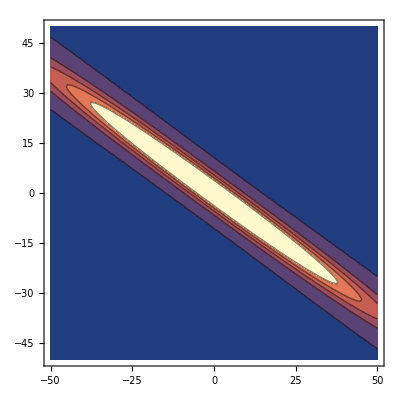

```mathematica
ContourPlot[(It[x um,yTst,z um,tTst,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst]/It[0 um,yTst,0 um,tTst,ω0Tst,ΔωTst,γTst,w0Tst,zcTst,ϕ2InTst]),{z,-zRange/um,zRange/um},{x,-xRange/um,xRange/um},PlotRange->All,PlotPoints->50,Contours->0.5{0.01,0.25,0.5,0.75,1}]
```

General::munfl: Exp[-1129.35] is too small to represent as a normalized machine number; precision may be lost.

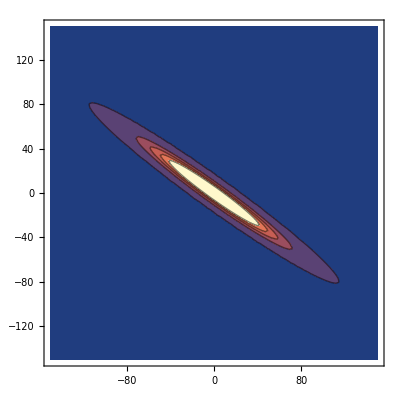

```mathematica
ContourPlot[(ItSimple[x um,yTst,z um,tTst,ω0Tst,τTst,γTst,w0Tst]),{z,-zRange/um,zRange/um},{x,-xRange/um,xRange/um},PlotRange->All,PlotPoints->50,Contours->0.5{0.01,0.25,0.5,0.75,1}]
```

#### define FFT and unwrap

```mathematica
FFT[fLst_,npts_,dt_]:=√((npts dt^2)/(2 π))RotateLeft[Fourier[RotateRight[fLst,npts/2]],npts/2];
InverseFFT[FLst_,npts_,dt_]:=√((2 π)/(npts dt^2))RotateLeft[InverseFourier[RotateRight[FLst,npts/2]],npts/2];
```

this version allows you to choose where the starting point is
phase is often noisy at edges of array, so start from center: dir = 0
dir = -1 start from left
dir = +1 start from right

```mathematica
unwrap[phs_,npts_,dir_]:=
Block[{phstmp},
phstmp=Table[1,{npts}];
Which[
dir==-1,
phstmp_⟦1⟧=phs_⟦1⟧;
shift=0;
For[i=2,i≤npts,i++,
If[(Abs[phs_⟦i-1⟧-phs_⟦i⟧]>2.5),
shift=shift+Sign[phs_⟦i-1⟧-phs_⟦i⟧] 2 π//N,
Null
];
phstmp_⟦i⟧=phs_⟦i⟧+shift;
],

dir==+1,
phstmp_⟦npts⟧=phs_⟦npts⟧;
shift=0;
For[i=npts-1,i≥1,i--,
If[(Abs[phs_⟦i+1⟧-phs_⟦i⟧]>2.5),
shift=shift+Sign[phs_⟦i+1⟧-phs_⟦i⟧] 2 π//N,
Null
];
phstmp_⟦i⟧=phs_⟦i⟧+shift;
],

dir==0,
phstmp_⟦npts/2⟧=phs_⟦npts/2⟧;
shift=0;
For[i=npts/2-1,i≥1,i--,
If[(Abs[phs_⟦i+1⟧-phs_⟦i⟧]>2.5),
shift=shift+Sign[phs_⟦i+1⟧-phs_⟦i⟧] 2 π//N,
Null
];
phstmp_⟦i⟧=phs_⟦i⟧+shift;
];
shift=0;
For[i=npts/2+1,i≤npts,i++,
If[(Abs[phs_⟦i-1⟧-phs_⟦i⟧]>2.5),
shift=shift+Sign[phs_⟦i-1⟧-phs_⟦i⟧] 2 π//N,
Null
];
phstmp_⟦i⟧=phs_⟦i⟧+shift;
]
];
    Return[phstmp]
];
```

```mathematica
FFTx[gLst_,npts_,dx_]:=√(npts dx^2)RotateLeft[Fourier[RotateRight[gLst,npts/2]],npts/2];
InverseFFTx[GLst_,npts_,dx_]:=√(1/(npts dx^2))RotateLeft[InverseFourier[RotateRight[GLst,npts/2]],npts/2];
```

#### define Gaussian beam parameters

note definition of w[ ] here has different parameters from wz[ ] defined above

```mathematica
zR[w0_,λ_,n_]:=n(π w0^2)/λ;
w[z_,w0_,λ_,n_]:=w0 √(1+z^2/zR[w0,λ,n]^2); (* z =0 at waist *)
zMin[wIn_,λ_,n_,f_]:=f/(1+f^2/zR[wIn,λ,n]^2);
wFoc[wIn_,λ_,n_,f_]:=wIn/(√(1+(zR[wIn,λ,n]/f)^2));
```

#### define input conditions

as defined below: x_0(z)=(z α Δω)/f=z/f β w_in. This is the centerline of the beamlet that is at the edge of the bandwidth.
at lens input, x_0=α Δω=β w_in, where Δω is the 1/e2 half width of the Gaussian spectral intensity
so α=β w_in/Δω

the beam aspect ratio as defined as the ratio of major/minor of the elliptical input beam:
β_BA=√(1+β^2)

τ0, δω is 1/e2 half width
δλ is FWHM

convert 1/e2 half width to FWHM:
e^(-2 (x_fwhm/2)^2/w^2)=1/2
x_fwhm^2/(2 w^2)=Log[2]
x_fwhm^2=2 w^2 Log[2]
x_fwhm=w √(2Log[2])
80nm = 10fs

wavelength scaling: 
for constant β, w_0, α=(β wIn)/δω0=(β τ)/2 2/π λ_0 f/(2 w_0)=β τ 1/π λ_0 f/(2 w_0)
need TF position <<zR
if zR>>f, calculated wIn won’t be right. try using gaussian beam formula for wIn(w0). 
PFT angle: 
φ(x,ω)=ω/c γ(ω-ω_0)x=γ ω^2/c x-γ ω/c ω_0 x
φ_1(x,ω)=2γ ω/c x-γ 1/c ω_0 x|_ω_0=γ ω_0/c x
Tan[θ_PF]=(c γ ω_0/c w_0)/w_0=γ ω_0
w_0=1/π λ f/w_in=2c λ/(2π c) f/w_in=(2c)/ω_0 f/w_in, (w_0 ω_0)/(2c)=f/w_in  
γ ω_0=α/f ω_0=(β w_in)/(f δω_0)ω_0=(β τ_0 2c)/(2 w_0 ω_0)ω_0=(β τ_0 c)/w_0
Tan[θ_PF]=γ ω_0=(β τ_0 c)/w_0

for input divergence of wavelengths:
γ_xin=α_x/f_x^2 f_0 θ_inc^2

```mathematica
runDisp=0;
λ0=800. nm;
ω0=(2 π)/λ0 c;
τ0=31.fs;
τFWHM =τ0 √(2 Log[2]);
δω0=2/τ0;
δλ0=(λ0 δω0/ω0)√(2 Log[2]);
Print["fund: pulse duration = ",τFWHM/fs," fs FWHM"];

fLens=1000.mm; (* keep this longer than zR *)
θcyl=27mrad;
fLensX=fLens Cos[θcyl];
fLensY=fLens/Cos[θcyl];
fLensX=fLens;
fLensY=fLens;

Print["transverse shift of focal spot from z-axis: ",fLensY Sin[2 θcyl]/mm," mm"];
w0=6.27um;
wIn=2/π λ0 fLens/(2 w0);
zR0=π w0^2/λ0;
Print["focal spot size: ",w0/um," microns"];
Print["fund calculated input beamlet spot 1/e2 radius: ",wIn/mm," mm"];
Print["fund beamlet Rayleigh range: ",zR0/mm," mm"];
Print["fund central wavelength: ",λ0/nm," nm"];
Print["astigmatic shift from nominal focal plane: ",(fLens-fLensX)/um," um"];
Print["out-of-focus spot size at other plane: ",w[fLensY-fLensX,w0,λ0,1]/um," um"];
```

fund: pulse duration = 36.4997 fs FWHM

transverse shift of focal spot from z-axis: 53.9738 mm

focal spot size: 6.27 microns

fund calculated input beamlet spot 1/e2 radius: 40.6137 mm

fund beamlet Rayleigh range: 0.154381 mm

fund central wavelength: 800. nm

astigmatic shift from nominal focal plane: 0. um

out-of-focus spot size at other plane: 6.27 um

```mathematica
(* BAR for input beam, based on measured beam width *)
βBA=5.; (* for input fundamental, 45deg *)
βBA=3.; (* for input fundamental, 45deg *)
β0 = √(βBA^2-1);
α0 = β0 wIn/δω0;
γIn=0α0 fLens/fLensX^2 θcyl^2;
γ0=-α0/fLensX;
θPF=ArcTan[(c τ0 β0)/w0];
```

```mathematica
Print["fund TL pulse duration: ",τFWHM /fs //N," fs"];
Print["fund bandwidth: ",δω0 fs//N," rad/fs"];

Print["fundamental fractional bandwidth: ",δλ0/λ0//N];

Print["fund spatial chirp rate β: ",β0//N];
Print["fund angular chirp rate γ0: ",γ0/fs," /(rad/fs)"];
Print["PFT angle: ",θPF/Degree," deg"];

Print["fund angular range: ",γ0 δω0/mrad," mrad = ",γ0 δω0/Degree," deg, F/#=",1/(2ArcTan[γ0 δω0])];
```

fund TL pulse duration: 36.4997 fs

fund bandwidth: 0.0645161 rad/fs

fundamental fractional bandwidth: 0.0322392

fund spatial chirp rate β: 2.82843

fund angular chirp rate γ0: -1.78053 /(rad/fs)

PFT angle: 76.593 deg

fund angular range: -114.873 mrad = -6.58173 deg, F/#=-4.37172

### test runs at ω0

#### set up t, x, y grids

```mathematica
npts=2^10;
dω=30. δω0/npts;
dt:=2 π/(npts dω);
tGridRange=npts dt/2;

timeLst=Table[t,{t,-(npts/2) dt,(npts/2-1) dt,dt}];
ωLst=Table[w+ω0,{w,-(npts/2) dω,(npts/2-1) dω,dω}];
λLst=2 π c/ωLst//N;
(*kLst=kzMedium[ωLst,ω0]; 
kTravLst=kLst-kzMedium[ω0,ω0]-kz1Medium[ω0,ω0](ωLst-ω0);
*)
nXpts=250;
xGridMin=-5w0;
xGridMax=5w0;
dx=(xGridMax-xGridMin)/nXpts;

xGridRange=nXpts dx/2;
xLst=Table[xGridMin+ix dx,{ix,1,nXpts}];

(*nYpts=200;
dy=5w0/nYpts;
yGridRange=nYpts dy/2;
yLst=Table[y,{y,-(nYpts/2) dy,(nYpts/2-1) dy,dy}];*)
```

```mathematica
Print["npts: ",npts];
Print["dt: ", dt/fs," fs"];
Print["time range: ±",tGridRange/ps," ps"];
Print["wavelength range from ",λLst[[npts]]/nm," to ",λLst[[1]]/nm," nm"];
Print["dx: ",dx/um," um"];
Print["x range: ±",xGridRange/um," μm"];
```

npts: 1024

dt: 3.24631 fs

time range: ±1.66211 ps

wavelength range from 567.408 to 1357.59 nm

dx: 0.2508 um

x range: ±31.35 μm

#### run x, t slice, fixed z position

τTst is a fixed group delay shift, to see if it moves the correct amount. 
currently, I’m finding the peak of the pulse in the time domain, then rolling all x points around - so we can’t see this shift

```mathematica
y0Tst=0mm;
zCtrTst=fLensX;
z0Tst=0.1um;
z0Tst=1.5zR0;
zTst=fLensY+z0Tst; 
ϕt2=00 fs^2;
ϕt3=0 fs^3;
γIn=0α0 fLens/fLensX^2 θcyl^2;

Print["z position from nominal focal plane: ",(zTst-fLensX)/um," um"];
Print["z position: rayleigh ranges from geometric focal plane ",(zTst-fLensX)/zR0];
Print["time delay: ",(zTst-fLensY)/c/fs," fs"];
(*τTst=0fs;*)
```

z position from nominal focal plane: 231.572 um

z position: rayleigh ranges from geometric focal plane 1.5

time delay: 771.907 fs

test crossed Gaussian beamlet version ω-space, FFT to t-space
   for positions away from focus, I’m getting underflow errors. Using Chop[ ] to get rid of them.

```mathematica
zcTst=0;
AxωFcn[x_]=ParallelTable[If[(ωLst[[iω]]-ω0)^2/δω0^2>10.,0,Aω[x,y0Tst,z0Tst,ωLst[[iω]],ω0,δω0,γ0,w0,zcTst,ϕt2]],{iω,1,npts}];
```

```mathematica
AxωLst=ParallelTable[If[xLst[[ix]]^2/w0^2>10,0,AxωFcn[xLst[[ix]] ]],{ix,1,nXpts}];
```

```mathematica
zcTst=0;
AxωFcn[x_]=ParallelTable[Aω[x,y0Tst,z0Tst,ωLst[[iω]],ω0,δω0,γ0,w0,zcTst,ϕt2],{iω,1,npts}];
```

```mathematica
AxωLst=ParallelTable[Chop[AxωFcn[xLst[[ix]] ]],{ix,1,nXpts}];
```

```mathematica
IxωLst=Chop[Abs[AxωLst]^2];
AbsoluteTiming[
AxtLst=ParallelTable[InverseFFT[AxωLst[[i]],npts,dt],{i,1,nXpts}];
]
IxtLst=Abs[AxtLst]^2;
IxMaxLst=IxTotLst=0Range[nXpts];
For[ix=1,ix≤nXpts,ix++,
IxMaxLst[[ix]]=Max[IxtLst[[ix]] ];
IxTotLst[[ix]]=Total[IxtLst[[ix]] ];
];
```

{0.155963,Null}

analytic t-domain test

```mathematica
zcTst=0;
IxtAnalyticLst=ParallelTable[ Abs[At[xLst[[ix]],y0Tst,z0Tst,timeLst,ω0,δω0,γ0,w0,zcTst,ϕt2]]^2,{ix,1,nXpts}];
```

plot x vs t

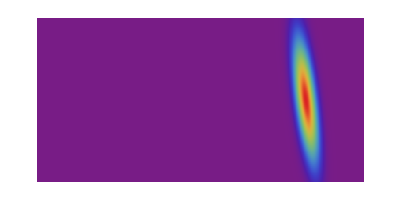

```mathematica
tRange=1200.0 fs;
itWindow=Round[tRange/dt];
ArrayPlot[Transpose[Take[Transpose[IxtLst],{npts/2-itWindow,npts/2+itWindow}]],ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1/2]
```

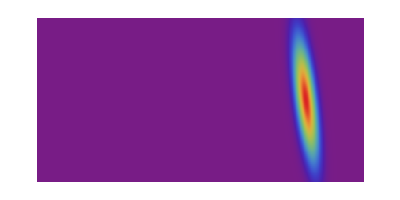

```mathematica
tRange=1200.0 fs;
itWindow=Round[tRange/dt];
ArrayPlot[Transpose[Take[Transpose[IxtAnalyticLst],{npts/2-itWindow,npts/2+itWindow}]],ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1/2]
```

compare local bandwidth (blue) to full (red)

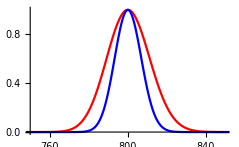

```mathematica
ixTst=nXpts/2;
ListLinePlot[{Transpose[{λLst/nm,Exp[-2(ωLst-ω0)^2/δω0^2]}],Transpose[{λLst/nm,IxωLst[[ixTst]]/Max[IxωLst]}]},PlotRange->{{750,850},All},PlotStyle->{Red,Blue}]
```

plot inten vs t at chosen x,z position
compare TL pulse (red) to actual (gray)

x position: -10.032 μm

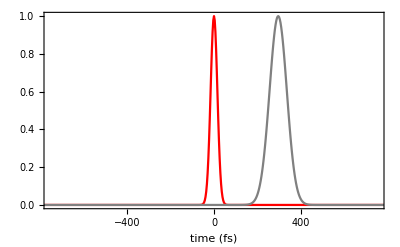

```mathematica
ixTst=nXpts/2-40 ;
tRange=750fs;
Print["x position: ", xLst[[ixTst]]/um," μm"];
tp0=ListLinePlot[{Transpose[{timeLst/fs,Exp[-2 timeLst^2/τ0^2]}],Transpose[{timeLst/fs,IxtLst[[ixTst]]/Max[IxtLst[[ixTst]]]}]},PlotRange->{{-tRange/fs,tRange/fs},All},PlotStyle->{Red,Gray},Frame->True,FrameLabel->{"time (fs)",None}]
```

for x, z position, plot pulse for numeric (gray) vs analytic (red)

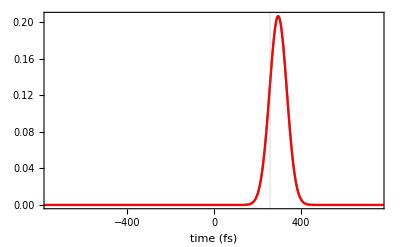

```mathematica
ixTst=nXpts/2-40 ;
tRange=750fs;
tp1=ListLinePlot[{
Transpose[{timeLst/fs,IxtAnalyticLst[[ixTst]]/Max[IxtAnalyticLst]}],
Transpose[{timeLst/fs,IxtLst[[ixTst]]/Max[IxtLst]}]},
PlotRange->{{-tRange/fs,tRange/fs},All},PlotStyle->{Gray,Red},Frame->True,FrameLabel->{"time (fs)",None},GridLines->{{(zTst-fLensY)/c/fs},None}]
```

```mathematica
ListPlot3D[Transpose[Take[Transpose[IxtLst/Max[IxtLst]-RotateRight[IxtAnalyticLst/Max[IxtAnalyticLst],{0,-0}]],{npts/2-itWindow,npts/2+itWindow}]],ColorFunction->"Rainbow",PlotRange->All]
```

-Graphics3D-

-Graphics3D-

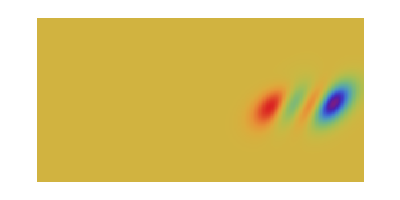

```mathematica
ArrayPlot[Transpose[Take[Transpose[IxtLst/Max[IxtLst]-RotateRight[IxtAnalyticLst/Max[IxtAnalyticLst],{0,-0}]],{npts/2-itWindow,npts/2+itWindow}]],ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1/2]
```